# Controlled Power

Episodes 17 and 19. ControlledGate

Episode 34. ControlledPower

Episode 35. Quantum Phase Estimation: Principle

Episode 36. Quantum Phase Estimation: Implementation

## What is it?

The controlled-power of unitary operator U is given by

x_1 x_2…x_n⊗ψ↦x_1 x_2…x_n⊗(U^x ψ) ,

where x:=(x_1 x_2(…x)_n)_2=x_1 2^(n-1)+x_2 2^(n-2)+…+x_n.

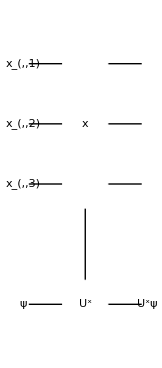

Figure 1. Quantum circuit for the controlled-power of unitary U, x_1 x_2…x_n⊗ψ↦x_1 x_2…x_n⊗(U^x ψ), where x:=(x_1 x_2(…x)_n)_2=x_1 2^(n-1)+x_2 2^(n-2)+…+x_n.

## Basic Example

```mathematica
Let[Qubit,S,T]
```

Consider a control register consisting of n qubits.

```mathematica
$n=3;
kk=Range[$n];
SS=S[kk,$]
```

Consider a single-qubit unitary gate acting on the target qubit.

```mathematica
Let[Real,ϕ]
opU=Phase[ϕ,T[3]]
```

Construct the controlled-power of opU defined above.

```mathematica
cop=ControlledPower[SS,opU]
```

Construct a simple quantum circuit to demonstrate how the controlled-power gate works.

```mathematica
qc=QuantumCircuit[
ProductState[T->{1,1}],
cop,
"Invisible"->S[$n+1/2],
"PortSize"->{2,1}
]
```

Take computational basis states as inputs.

```mathematica
in=Basis[SS]
```

Calculate the output for each input state.

```mathematica
out=qc**in
```

```mathematica
Thread[in->KetFactor[out]]//TableForm
```

## More Interesting Example

Construct a simple quantum circuit to demonstrate how the controlled-power gate works.

```mathematica
qc=QuantumCircuit[
Ket[SS->0,T->1],
S[kk,6],"Separator",cop,
"Invisible"->S[$n+1/2],
"PortSize"->{2,1}
]
```

Calculate the output state.

```mathematica
out=Elaborate[qc]
```

Check that the target qubit is factorized.

```mathematica
KetFactor[out,T]
```

To focus on the state of the control register, ignore the target qubit.

```mathematica
KetDrop[out,T]
```

## Implementation with Elementary Gates

Consider again  the quantum circuit for controlled-power gate.

```mathematica
qc=QuantumCircuit[cop,"Invisible"->S[$n+1/2]]
```

Expand the controlled-power gate in terms of elementary gates (in this case, the controlled-unitary gates).

```mathematica
new=Expand[qc]
```

```mathematica
Matrix[qc]-Matrix[new]//MatrixForm
```

## Summary

### Keywords

Controlled-power of unitary operator

Controlled-unitary gate

### Functions

ControlledPower

ControlledGate

### Related Links

Section 4.3 of the Quantum Workbook (2022, 2023).

Tutorial: Quantum Phase Estimation